# HRI and the SFS

## Parameters

## Formulae

### Get Ne

```mathematica
U=L u
```

L u

```mathematica
Vm=U s^2
```

L s^2 u

```mathematica
γ0=2NN s
```

2 NN s

```mathematica
α0=2NN U
```

2 L NN u

```mathematica
γ=2B γ0
```

4 B NN s

Gamma0 here too?

```mathematica
Vg=(U s(1-Exp[-γ0]))/(1+κ Exp[-γ0])
```

((1-ⅇ^(-2 NN s)) L s u)/(1+ⅇ^(-2 NN s) κ)

Eq 3

```mathematica
eq3=(Vg^3/Vm^2/.NN->(B NN))+Log[B]
```

((1-ⅇ^(-2 B NN s))^3 L u)/(s (1+ⅇ^(-2 B NN s) κ)^3)+Log[B]

```mathematica
getPbar[kk_,ss_,NN_]:=1/(1+kk Exp[-2NN ss])
```

```mathematica
getGammaHat[kk_,pBar_]:=Log[(kk pBar)/(1-pBar)]
```

Expected p bar

```mathematica
getPbar[1,10^-4,1000]//N
```

0.549834

```mathematica
getGammaHat[1,#]&/@{0.529,0.533,0.537}
```

{0.11613,0.132192,0.148271}

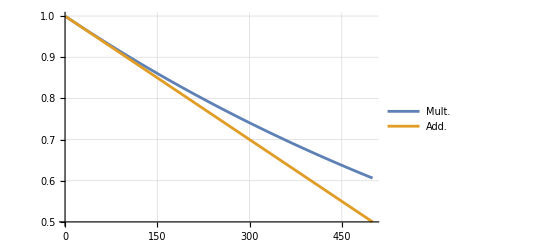

```mathematica
Plot[{(.999)^x,1-(1-0.999)x},{x,1,500},GridLines->Automatic,PlotLegends->{"Mult.", "Add."}]
```

```mathematica
getGammaHat[1,1-Log[0.955]/Log[0.9999]/1000]
```

0.158667

```mathematica
getGammaHat[1,0.536]
```

0.14425

```mathematica
0.9999^550
```

0.946483

```mathematica
params1={NN->1000,s->10^-4,κ->1,L->2500,u->10^-5}
```

{NN→1000,s→1/10000,κ→1,L→2500,u→1/100000}

```mathematica
params2={NN->1000,s->10^-3,κ->1,L->40000,u->10^-5}
```

{NN→1000,s→1/1000,κ→1,L→40000,u→1/100000}

```mathematica
eq302=eq3/.params2
```

(400 (1-ⅇ^(-2 B))^3)/((1+ⅇ^(-2 B))^3)+Log[B]

```mathematica
bfun02[a_]:=eq302/.B->a
```

```mathematica
bfun02[.02]
```

-3.90882

```mathematica
Clear[newtonRoot]
```

```mathematica
newtonRoot[fun:_Symbol|_Function, init_Real, tol_:1.*^-10]:=
Module[{funp},funp=Derivative[1][fun];
NestWhile[#-fun[#]/funp[#]&,init,Abs[Subtract[##]]>=tol&,2]
]
```

May need to adjust starting value (2nd argument) if this fails:

```mathematica
bsel02=newtonRoot[bfun02[#]&,0.2]
```

0.16641

```mathematica
pbarExp02=getPbar[1,10^-3,1000 bsel02]
```

0.582446

### Get Ne trajectory for neutral sites

```mathematica
Qt=(Vg/Vm (1-1(1-Vm/Vg)^(τ+1)))
```

((1-ⅇ^(-2 NN s)) (1-(1-(s (1+ⅇ^(-2 NN s) κ))/(1-ⅇ^(-2 NN s)))^(1+τ)))/(s (1+ⅇ^(-2 NN s) κ))

```mathematica
params2
```

{NN→1000,s→1/1000,κ→1,L→10000,u→1/100000}

```mathematica
Nprime[B_,params_]:=
NN/Exp[(Vg /.NN->(NN B)) (Qt/.NN->(NN B))^2]/.params
```

```mathematica
np02=Nprime[bsel02,params2]
```

1000 ⅇ^(-1.7933 (1-0.993935^(1+τ))^2)

```mathematica
np02/.τ->#&/@{0, 500,1000,1500,2000}
```

{999.934,196.503,167.768,166.475,166.414}

#### Ne plots

```mathematica
Nprime01=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-8//Simplify
```

10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3))

```mathematica
Nprime02=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-7//Simplify
```

10000 ⅇ^(-19200/49331-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Nprime03=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-6//Simplify
```

10000 ⅇ^(-1920000/4801331-(10 (-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Plot[{Nprime01/.τ->x,Nprime02/.τ->x,Nprime03/.τ->x},{x,0,100000}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8","u=10^-7","u=10^-6"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

```mathematica
Plot[{NprimeSc01/.τ->x},{x,0,10}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

#### Expressions from Polanski and Kimmel. 2003

The calculations below follow the approach of Polanski, A., and Kimmel, M. (2003). New Explicit Expressions for Relative Frequencies of Single-Nucleotide Polymorphisms With Application to Statistical Inference on Population Growth.” Genetics 165:427–436. The equation numbers used by Polanski and Kimmel (2003) are indicated here and in the exponential growth section.

Equation 6 (coefficient used in equations 9 and 10):

```mathematica
Akjn[k_,j_,n_]:=Product[Binomial[l,2],{l,Select[Range[k,n],#≠j&]}]/Product[Binomial[l,2]-Binomial[j,2],{l,Select[Range[k,n],#≠j&]}]
```

Equation 9 (coefficient used in equation 8):

```mathematica
vnj[n_,j_]:=Sum[j(j-1)Akjn[k,j,n]/(k-1),{k,2,j}]
```

Equation 10 (coefficient used in equation 8):

```mathematica
wnbj[n_,b_,j_]:=Sum[j(j-1)Binomial[n-k,b-1]((n-b-1)!(b-1)!)/((n-1)!)Akjn[k,j,n],{k,2,j}]
```

### Doing it on HRI

#### Piecewise approx

*Get extrema from Brian’s message
* get inverse with respect to τ
* make τ intervals so that the Δy are equal

```mathematica
kk=1
```

1

```mathematica
nPrimeAndLimits[ee_]:=
{ee, ee/.τ->0,ee/.τ->∞}
```

Should s be pos or neg? Either give reasonable trajectories.

```mathematica
rAndL=nPrimeAndLimits[np02];
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.7933 (1-0.993935^(1+τ))^2),999.934,166.41}

```mathematica
{x->#,y->rAndL⟦1⟧/.τ->#}&/@Range[0,5000,500]//N
```

```mathematica
{{x->0.,y->999.9758849338513},{x->500.,y->341.47926284834415},{x->1000.,y->256.92444267278876},{x->1500.,y->247.3500977052783},{x->2000.,y->246.16752998190728},{x->2500.,y->246.01970478874085},{x->3000.,y->246.0011980558869},{x->3500.,y->245.99888069501498},{x->4000.,y->245.99859051471174},{x->4500.,y->245.99855417817884},{x->5000.,y->245.99854962809712}}
```

{{x→0.,y→999.976},{x→500.,y→341.479},{x→1000.,y→256.924},{x→1500.,y→247.35},{x→2000.,y→246.168},{x→2500.,y→246.02},{x→3000.,y→246.001},{x→3500.,y→245.999},{x→4000.,y→245.999},{x→4500.,y→245.999},{x→5000.,y→245.999}}

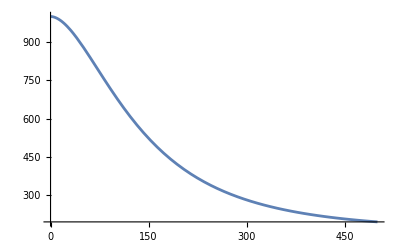

```mathematica
Plot[rAndL⟦1⟧,{τ,0,500}]
```

```mathematica
getInv[ral_]:=Solve[{ral⟦1⟧==y},τ]
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.7933 (1-0.993935^(1+τ))^2),999.934,166.41}

```mathematica
inv=getInv[rAndL];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
inv/.y->660//N
```

{{τ→106.929},{τ→-65.5987}}

```mathematica
inv
```

{{τ→-164.391 Log[1.41835×10^-16 (7.09348×10^15-1. √(5.03175×10^31-2.80586×10^31 Log[0.00600923706156058 y]))]},{τ→-164.391 Log[1.418346603568×10^-16 (7.0934819909335×10^15+√(5.0317486755698×10^31-2.8058634141833×10^31 Log[0.00600923706156058 y]))]}}

```mathematica
inv2=inv⟦1,1,2⟧
```

-164.391 Log[1.41835×10^-16 (7.09348×10^15-1. √(5.03175×10^31-2.80586×10^31 Log[0.00600923706156058 y]))]

```mathematica
inv2/.y->660//N
```

106.929

#### Breaks, even x steps

```mathematica
getXs[ral_,n_,inv_]:=Module[{fiveP=(ral⟦2⟧-ral⟦3⟧)/20+ral⟦3⟧},
Subdivide[0,inv/.y->fiveP,n]
]
```

```mathematica
xs=getXs[rAndL,10,inv2];
```

```mathematica
xs//N
```

{0.,14.6332,29.2663,43.8995,58.5327,73.1658,87.799,102.432,117.065,131.699,146.332}

```mathematica
{1,2,3,4,5}+1/2
```

{3/2,5/2,7/2,9/2,11/2}

```mathematica
getYs[xs_,ral_]:=Module[{dd=xs⟦2⟧-xs⟦1⟧},
Join[{ral⟦2⟧},ral⟦1⟧/.τ->#&/@((xs//Rest//Most)+dd/2),{ral⟦3⟧}]
]
```

```mathematica
ys=getYs[xs,rAndL];
```

```mathematica
ys//N
```

{999.363,786.848,594.823,441.552,332.31,257.358,206.178,170.87,146.113,128.443,75.327}

```mathematica
xy1={xs,ys}//N
```

{{0.,14.6332,29.2663,43.8995,58.5327,73.1658,87.799,102.432,117.065,131.699,146.332},{999.363,786.848,594.823,441.552,332.31,257.358,206.178,170.87,146.113,128.443,75.327}}

#### Breaks, even y steps

```mathematica
getEquiDistYs[ral_,n_,inv_]:=Module[{
ys=Join[{ral⟦2⟧},ral⟦2⟧-Range[1,n-1](ral⟦2⟧-ral⟦3⟧)/n,{ral⟦3⟧}]},
{Join[{0},inv/.y->#&/@(Most[ys]-((ral⟦2⟧-ral⟦3⟧)/n/2))],ys}
]
```

```mathematica
xy2=getEquiDistYs[rAndL,10,inv2]//N
```

{{0.,26.5302,51.4094,72.6332,93.9158,116.967,143.523,176.226,220.298,289.49,449.897},{999.934,916.582,833.229,749.877,666.525,583.172,499.82,416.468,333.115,249.763,166.41}}

#### Return to function

```mathematica
Nprime01p=D[rAndL⟦1⟧,τ]
```

-21.8175 0.993935^(1+τ) (1-0.993935^(1+τ)) ⅇ^(-1.7933 (1-0.993935^(1+τ))^2)

```mathematica
Nprime01p/.τ->-10//N
```

1.28951

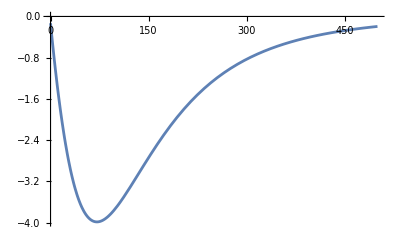

```mathematica
Plot[Nprime01p/.τ->t,{t,0,500}]
```

Assuming Nprime is monotonously decreasing, take values as x=0 and limit for x→∞

```mathematica
makePiecewiseTraj[xys_]:=Module[{pRules0={n,x<a}/.a->#1/.n->#2&@@@Transpose[{Rest[xys⟦1⟧],Most[xys⟦2⟧]}]},
Piecewise[Join[pRules0,{{Last[xys⟦2⟧],x>Last[xys⟦1⟧]}},{{0,True}}]//N]]
```

```mathematica
pwNe1=makePiecewiseTraj[xy1]
```

Part::partd: Part specification xy1⟦1⟧ is longer than depth of object.

Part::partd: Part specification xy1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Piecewise::pairs: The first argument {1.,xy1,{2.,x>1.},{0.,True}} of Piecewise is not a list of pairs.

Piecewise[N[Join[pRules0$7212,{{Last[xy1⟦2⟧],x>Last[xy1⟦1⟧]}},{{0,True}}]]]

```mathematica
pwNe2=makePiecewiseTraj[xy2]
```

Piecewise[{{999.934, x<26.5302}, {916.582, x<51.4094}, {833.229, x<72.6332}, {749.877, x<93.9158}, {666.525, x<116.967}, {583.172, x<143.523}, {499.82, x<176.226}, {416.468, x<220.298}, {333.115, x<289.49}, {249.763, x<449.897}, {166.41, x>449.897}, {0., True}}]

Piecewise::pairs: The first argument {1.,xy1,{2.,x>1.},{0.,True}} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {1.,xy1,{2.,False},{0.,True}} of Piecewise is not a list of pairs.

General::stop: Further output of Piecewise::pairs will be suppressed during this calculation.

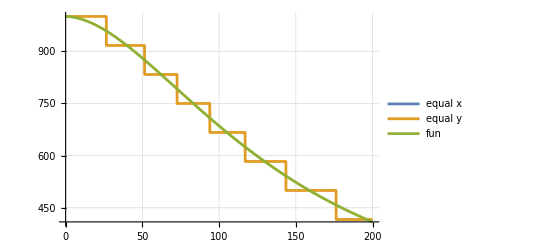

```mathematica
Plot[{pwNe1/.x->t,pwNe2/.x->t,rAndL⟦1⟧/.τ->t},{t,0,200},GridLines->Automatic,ImageSize->400,PlotLegends->{"equal x","equal y","fun"}]
```

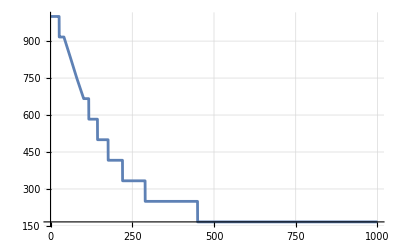

```mathematica
Plot[pwNe2/.x->t,{t,0,1000},GridLines->Automatic,ImageSize->400]
```

```mathematica
pwNe=pwNe2
```

Piecewise[{{999.934, x<26.5302}, {916.582, x<51.4094}, {833.229, x<72.6332}, {749.877, x<93.9158}, {666.525, x<116.967}, {583.172, x<143.523}, {499.82, x<176.226}, {416.468, x<220.298}, {333.115, x<289.49}, {249.763, x<449.897}, {166.41, x>449.897}, {0., True}}]

```mathematica
pwNe/.x->1000//N
```

166.41

```mathematica
qjtHriPw01[j_]:=Binomial[j,2]/pwNe Exp[-Integrate[Binomial[j,2]/(pwNe/.x->σ),{σ,0,x},Assumptions->x∈]]
```

Prob of coalescence for a pair of lineages at given time:

```mathematica
qjtHriPw01[2]/.x-> 600//N//AbsoluteTiming
```

{1.2687,0.0000189017}

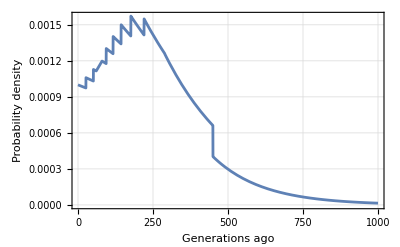

```mathematica
Plot[qjtHriPw01[2],{x,0,1000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHriPw[j_]:=Integrate[x qjtHriPw01[j],{x,0,∞}, Assumptions->x∈Reals]
```

Expected coalescence time for a pair of lineages.

2 steps 1.4s, 2 steps 3.2s, 4 steps 13s, 5 steps 62s

Is is much faster to use Integrate[] with Assumptions→x∈Reals than PiecewiseIntegrate[]:
5steps 10s, 8steps 18s,9 steps 21s

```mathematica
a01=(ejHriPw[2]//AbsoluteTiming)
```

{11.7597,351.388}

```mathematica
a01[[2]]
```

167.245

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHriPw[n_,b_]:=Sum[ejHriPw[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHriPw[j]vnj[n,j],{j,2,n}]
```

```mathematica
n10All=AbsoluteTiming[n10b1=qnbHriPw[10,#]]&/@Range[1,9]
```

{{151.378,0.510318},{122.747,0.181111},{121.911,0.0967257},{121.326,0.0623467},{120.802,0.0447458},{119.794,0.0343833},{119.504,0.0276783},{119.205,0.023036},{118.911,0.0196549}}

```mathematica
Export["v06sfs10.txt", n10All]
```

v06sfs10.txt

```mathematica
n20All=AbsoluteTiming[n20b1=qnbHriPw[20,#]]&/@Range[1,19]
```

{{294.757,0.43841},{261.287,0.168309},{260.997,0.0926352},{260.75,0.0600934},{260.395,0.0429203},{260.082,0.032659},{260.015,0.0259869},{259.883,0.0213731},{259.547,0.0180294},{259.741,0.0155151},{259.636,0.0135673},{259.455,0.012021},{259.442,0.010768},{259.274,0.00973507},{259.183,0.0088707},{259.107,0.00813805},{258.947,0.00751005},{258.825,0.00696641},{258.651,0.00649165}}

```mathematica
Export["v06sfs20.txt", n20All]
```

v06sfs20.txt

```mathematica
n40All=AbsoluteTiming[n40b1=qnbHriPw[40,#]]&/@Range[1,39]
```

{{607.723,0.379241},{542.064,0.157188},{541.428,0.0903606},{541.475,0.0600599},{541.542,0.0434371},{541.706,0.0332211},{541.468,0.0264442},{541.565,0.0216927},{541.554,0.0182178},{541.396,0.0155904},{541.102,0.0135492},{541.038,0.0119275},{541.222,0.0106145},{541.238,0.00953404},{541.477,0.0086325},{541.326,0.00787099},{541.614,0.00722081},{541.402,0.00666038},{541.386,0.00617318},{541.308,0.00574639},{541.361,0.00536995},{541.676,0.00503582},{541.593,0.00473756},{541.497,0.00446993},{541.661,0.00422863},{541.69,0.00401011},{541.143,0.00381143},{541.442,0.00363009},{541.005,0.003464},{540.749,0.0033114},{540.806,0.00317075},{540.718,0.00304075},{540.678,0.00292028},{540.747,0.00280836},{540.899,0.00270415},{540.953,0.00260688},{541.178,0.00251593},{541.082,0.0024307},{541.034,0.00235068}}

```mathematica
Export["v06sfs40.txt", n40All]
```

v06sfs40.txt

```mathematica
n80All=AbsoluteTiming[n80b1=qnbHriPw[80,#]]&/@Range[1,79]
```

{{1313.43,0.327691},{1192.57,0.14485},{1189.05,0.0870067},{1187.74,0.0596489},{1187.17,0.0441095},{1187.34,0.0342796},{1188.93,0.0275994},{1188.52,0.0228198},{1186.32,0.0192646},{1186.33,0.0165381},{1186.67,0.0143952},{1186.7,0.0126762},{1187.29,0.0112734},{1186.67,0.0101118},{1186.43,0.00913767},{1186.73,0.00831159},{1186.81,0.00760419},{1186.64,0.0069931},{1186.6,0.00646107},{1186.29,0.00599461},{1186.47,0.005583},{1186.28,0.00521769},{1186.31,0.00489174},{1186.77,0.00459948},{1188.,0.00433626},{1188.32,0.00409819},{1185.37,0.00388206},{1185.99,0.00368512},{1186.19,0.00350508},{1186.1,0.00333998},{1186.09,0.00318812},{1186.12,0.00304807},{1185.84,0.00291858},{1185.88,0.00279855},{1186.04,0.00268705},{1185.41,0.00258324},{1185.16,0.00248639},{1185.34,0.00239586},{1185.18,0.00231109},{1185.15,0.00223156},{1185.18,0.00215684},{1185.49,0.00208651},{1185.26,0.00202022},{1185.06,0.00195766},{1185.27,0.00189852},{1185.33,0.00184255},{1185.12,0.0017895},{1185.15,0.00173918},{1186.06,0.00169138},{1185.49,0.00164592},{1185.52,0.00160265},{1186.29,0.00156141},{1186.34,0.00152208},{1185.89,0.00148452},{1185.78,0.00144864},{1185.74,0.00141431},{1185.85,0.00138145},{1185.69,0.00134997},{1185.66,0.00131979},{1185.8,0.00129082},{1185.72,0.00126301},{1185.81,0.00123628},{1185.3,0.00121058},{1185.08,0.00118585},{1185.33,0.00116204},{1185.48,0.0011391},{1185.33,0.00111698},{1185.18,0.00109564},{1185.12,0.00107505},{1185.21,0.00105517},{1185.3,0.00103595},{1185.35,0.00101738},{1185.1,0.000999412},{1185.24,0.000982026},{1184.96,0.000965194},{1184.92,0.00094889},{1185.07,0.000933091},{1185.12,0.000917775},{1184.79,0.000902919}}

```mathematica
Export["v06sfs80.txt", n80All]
```

v06sfs80.txt

```mathematica
sfs01=#⟦2⟧&/@n12All
```

{0.413224,0.177479,0.105818,0.0728697,0.0545042,0.0430248,0.035276,0.0297467,0.0256311,0.0224646,0.0199623}

```mathematica
#⟦2⟧&/@n12All//Total
```

1.

Expected π is ejHriPw[2] × 2 × μ

```mathematica
a01⟦2⟧
```

599.115

```mathematica
piUncond[T_,u_,κ_]:=2T 2u u κ/(u+u κ)
```

```mathematica
piUncond01=piUncond[a01⟦2⟧,10^-5,1]
```

0.0119823

```mathematica
(1+kk)  10^-5
```

(1+kk)/100000

```mathematica
condPi[sfs_]:=Module[{n=Length[sfs]+1},
∑_(i=1)^(n-1) 2i(n-i)sfs⟦i⟧/n^2
]
```

```mathematica
condPi01=condPi[sfs01]
```

0.281777

```mathematica
an[n_]:=∑_(i=1)^(n-1) 1/i
```

```mathematica
an[12]
```

83711/27720

```mathematica
an[Length[sfs01]+1]
```

83711/27720

Δθ

```mathematica
1-condPi[sfs01]an[Length[sfs01]+1]
```

0.149067

```mathematica
thetaw01=piUncond01/condPi01/an[12]
```

0.0140814

```mathematica
1-piUncond01/thetaw01
```

0.149067

```mathematica
Length[sfs01]
```

11

#### Comeron 2002 params

Their α is our γ,
their β is Ne×μ with μ=(w+v), i.e. per-nuc. rates to del and back, respectively
Their w is our u, their v is our κu
Their γ is related to our κ:
γ_Com=v/(w+v)=κu/(u+κu)
Thus, κ=γ/(1-γ)
Their defaults are γ=0.45 and β_N=0.01, i.e.

```mathematica
.45/(1-.45)
```

0.818182